{X+GNAY →^1. XGNAY ,XGNAY →^1. X+GNAY ,XGNAY →^60. XGNAY+TSAY ,TSAY →^1. TSAY+AY ,TSAY →^5. 0 ,AY →^1. 0 ,conc[X,10],conc[GNAY,1],t$125927+GNTY →^1. t$125927GNTY ,t$125927GNTY →^1. t$125927+GNTY ,t$125927GNTY →^60. t$125927GNTY+TSTY ,TSTY →^1. TSTY+TY ,TSTY →^5. 0 ,TY →^1. 0 ,conc[t$125927,5],conc[GNTY,1],TY+AY →^1000 0 ,AY+GNY →^110 AYGNY ,AYGNY →^25 AY+GNY ,AYGNY →^60. AYGNY+TSY ,TSY →^1. TSY+Y ,TSY →^5. 0 ,Y →^1. 0 ,conc[AY,0],conc[GNY,1]}

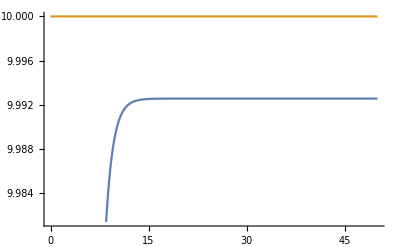

```mathematica
Clear[GRN]
GRN[{IN_,OUT_},init_:{x[0]==0},kON_:1.0,kOFF_:1.0]:=(
With[
{c=
Cases[init,v_[0]== b_ ->b]},
initIN=c[[1]]];
ktx=60.0;
ktl=kpd=1.0;
krd=5.0;
Gtot=1;
out=ToString[OUT];
in=ToString[IN];
gn=Symbol["GN"<>out];
ts=Symbol["TS"<>out];
actGene=Symbol[in<>ToString[gn]];
Seq[
revrxn[IN+gn,actGene,kON,kOFF],
rxn[actGene,actGene+ts,ktx],
rxn[ts,ts+OUT,ktl],
rxn[ts,0,krd],
rxn[OUT,0,kpd],

conc[IN,initIN],
conc[gn,Gtot]
]
)

Clear[titrationGRN]
titrationGRN[{IN_,OUT_},init_:{x[0]==0}]:=Module[{null,initT,rptrON,rptrOFF,kc,t,in,out,titr,anyl},
in=ToString[IN];
out=ToString[OUT];
titr=Symbol["T"<>out];
anyl=Symbol["A"<>out];
rptrON=110;
rptrOFF=25;
kc=1000;
Seq[
(* analyte *)
GRN[{IN,anyl},init],

(* titrant *)
GRN[{t,titr},{t[0]==5}],

(* titrant rxn *)
rxn[titr+anyl,0,kc],

(* reporter *)
GRN[{anyl,OUT},{anyl[0]==0},rptrON,rptrOFF]
]
]
Clear[X,Y];
tmax=50;
dummySys2={
titrationGRN[{X,Y},{X[0]==10}]
}
sol=SimulateRxnsys[dummySys2,tmax];
plotter={Y[t]}/.sol;
Plot[{plotter,10},{t,0,50}]
```

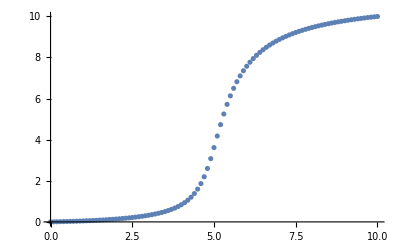

```mathematica
Clear[A,B]

GRNSim[GRN_,watch_,time_]:=(
rsys=Flatten[GRN];

sol=SimulateRxnsys[rsys,time];
plotter=(#[t]&/@watch)/.sol
)


GRNSimPlot[GRN_,watch_,time_]:=(
rsys=Flatten[GRN];
sol=SimulateRxnsys[rsys,time];
plotter=(#[t]&/@watch)/.sol;
Plot[plotter,{t,0,time},PlotRange->All,
PlotLegends->watch]
)

tmax=20;
y=Table[{i,GRNSim[{titrationGRN[{A,B},{A[0]==i}]},{B},tmax][[1]][[0]][tmax]},{i,0,10,0.1}];
ListPlot[y]
```

```mathematica
Clear[GRN]
GRN[{IN_,OUT_},init_:{x[0]==0},kON_:1.0,kOFF_:1.0]:=(
With[
{c=
Cases[init,v_[0]== b_ ->b]},
initIN=c[[1]]];
Gtot=1;
out=ToString[OUT];
in=ToString[IN];
gn=Symbol["GN"<>out];
ts=Symbol["TS"<>out];
actGene=Symbol[in<>ToString[gn]];
Seq[
revrxn[IN+gn,actGene,kON,kOFF],
rxn[actGene,actGene+ts,ktx],
rxn[ts,ts+OUT,ktl],
rxn[ts,0,krd],
rxn[OUT,0,kpd],

conc[IN,initIN],
conc[gn,Gtot]
]
)

Clear[titrationGRN]
titrationGRN[{IN_,OUT_},init_:{x[0]==0}]:=(
in=ToString[IN];
out=ToString[OUT];
titr=Symbol["T"<>out];
anyl=Symbol["A"<>out];
rptrON=110;
rptrOFF=25;
Seq[
(* analyte *)
GRN[{IN,anyl},init],

(* titrant *)
GRN[{TR,titr},{TR[0]==5}],

(* titrant rxn *)
rxn[titr+anyl,0,kc],

(* reporter *)
GRN[{anyl,OUT},{anyl[0]==0},rptrON,rptrOFF]
]

)
```

```mathematica
dummySys2={
titrationGRN[{X,Y},{X[0]==10}]
};

tmax=20;
sol=SimulateRxnsys[dummySys2/.{ktx->60.0,ktl->1.0,kpd->1.0,krd->5.0,kc->1000},tmax];
```

```mathematica
?/.
```

expr/.rules applies a rule or list of rules in an attempt to transform each subpart of an expression expr.

```mathematica
x+y+z/.{x->1,y->2,z->3}
```

6

```mathematica
x+y+z
```

x+y+z

```mathematica
GRNSim1[GRN_,watch_,time_]:=(
rsys=Flatten[GRN];

sol=SimulateRxnsys[rsys,time];
plotter=(#[t]&/@watch)/.sol
)


GRNSimPlot1[GRN_,watch_,time_]:=(
rsys=Flatten[GRN];
sol=SimulateRxnsys[rsys,time];
plotter=(#[t]&/@watch)/.sol;
Plot[plotter,{t,0,time},PlotRange->All,
PlotLegends->watch]
)



tmax=20;
Manipulate[GRNSimPlot1[{titrationGRN[{X,Y},{X[0]==i}],titrationGRN[{Y,Z},{Y[0]==0}]},{Z},tmax],{i,0,10}]
```

```mathematica
dummySys={
titrationGRN[{X,Y},{X[0]==5}],titrationGRN[{Z,Y},{Z[0]==5}]}
```

{X+GNAY →^1. XGNAY ,XGNAY →^1. X+GNAY ,XGNAY →^60. XGNAY+TSAY ,TSAY →^1. TSAY+AY ,TSAY →^5. null$42007 ,AY →^1. null$42007 ,conc[X,5],conc[GNAY,1],t$42006+GNTY →^1. t$42006GNTY ,t$42006GNTY →^1. t$42006+GNTY ,t$42006GNTY →^60. t$42006GNTY+TSTY ,TSTY →^1. TSTY+TY ,TSTY →^5. null$42008 ,TY →^1. null$42008 ,conc[t$42006,5],conc[GNTY,1],TY+AY →^1000 null$42006 ,AY+GNY →^110 AYGNY ,AYGNY →^25 AY+GNY ,AYGNY →^60. AYGNY+TSY ,TSY →^1. TSY+Y ,TSY →^5. null$42009 ,Y →^1. null$42009 ,conc[AY,0],conc[GNY,1],Z+GNAY →^1. ZGNAY ,ZGNAY →^1. Z+GNAY ,ZGNAY →^60. ZGNAY+TSAY ,TSAY →^1. TSAY+AY ,TSAY →^5. null$42011 ,AY →^1. null$42011 ,conc[Z,5],conc[GNAY,1],t$42010+GNTY →^1. t$42010GNTY ,t$42010GNTY →^1. t$42010+GNTY ,t$42010GNTY →^60. t$42010GNTY+TSTY ,TSTY →^1. TSTY+TY ,TSTY →^5. null$42012 ,TY →^1. null$42012 ,conc[t$42010,5],conc[GNTY,1],TY+AY →^1000 null$42010 ,AY+GNY →^110 AYGNY ,AYGNY →^25 AY+GNY ,AYGNY →^60. AYGNY+TSY ,TSY →^1. TSY+Y ,TSY →^5. null$42013 ,Y →^1. null$42013 ,conc[AY,0],conc[GNY,1]}

You take the sum of all concentrations (!!)

{a →^0.35 b ,a →^0.35 b ,conc[a,1]}

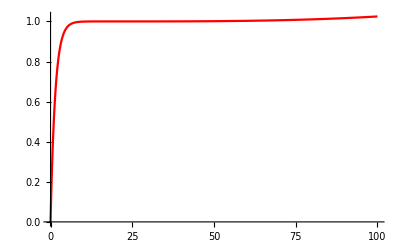

```mathematica
Clear[a,b]
rsys={
rxn[a,b,0.35],
rxn[a,b,0.35],

conc[a,1]
}
tmax=20;
sol=SimulateRxnsys[rsys,tmax];
plotter={b[t]}/.sol;
Plot[plotter,{t,0,100},PlotRange->All,PlotStyle->{Red}]
```

{a →^0.4 b ,conc[a,1]}

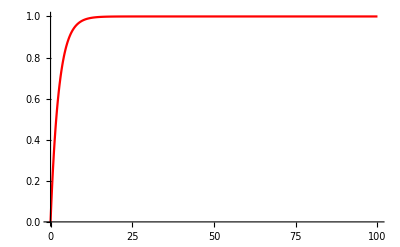

```mathematica
Clear[a,b]
rsys={
rxn[a,b,0.4],

conc[a,1]
}
tmax=100;
sol=SimulateRxnsys[rsys,tmax];
plotter={b[t]}/.sol;
Plot[plotter,{t,0,100},PlotRange->All,PlotStyle->{Red}]
```

```mathematica
rsys={
rxn[a,b,0.35],
rxn[a,b,0.35],

conc[a,1]
};

DeleteDuplicates[rsys]
```